A basic framework for an election simulator 
You are welcome to use this code as a starting point or as inspiration for your work for the election project.

```mathematica
Remove["Global`*"]
U:=Random[]

Z:=√(-2 Log[U]) Cos[2 π U]
Data=Table[Z,{10000}];
Data
```

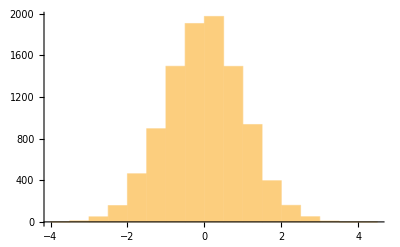

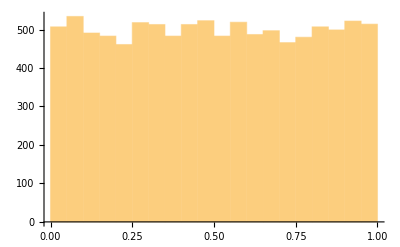

```mathematica
Histogram[Table[Z,{10000}]]
Histogram[Table[U,{10000}]]
```

```mathematica
weights={0.2,0.3,0.5};
(*list contains the result for the past three election cycles, with 0 for red and 1 for blue*)
vectorsList={{0,1,1},(*oh*){1,1,1}   (*ga*)
(*Add more states here if from the swing states list.make up data for them now*)};
weightedSums=Total[#*weights]&/@vectorsList;
weightedSums
```

{0.8,1.}

```mathematica
assignVotes[b_,r_,v_]:=Module[{},
(* determine whether red or blue gets the EVs *)
If[Z<0,red+=v,blue+=v]  (* <-- this is a pure coinflip and ignores all polling *)
]
(*Margin of error - 3-4%*)
```

```mathematica
(* assign swing state votes based on polling -- your swing states may be different *)
(*What if --> most important swing state*)
OH:=assignVotes[36,47,17]
GA:=assignVotes[43,49,16](*Not a swing state anymore*)
WI:=assignVotes[37,41,10]
MI:=assignVotes[43,43,15]
PA:=assignVotes[40,39,19] (**)
AZ:=assignVotes[40,47,11]
CO:=assignVotes[44,48,9]
NV:=assignVotes[34,44,6]
VA:=assignVotes[49,42,13]
AZ:=assignVotes[40,47,11]
CT:= assignVotes[49,40,7]
IL:= assignVotes[53,47,19]
ME:= assignVotes[32,38,4]
MN:=assignVotes[46,39,10]
NH:= assignVotes[44,41,4]
NM:= assignVotes[49,41,5]
NC:=assignVotes[40,53,16]
VI:= assignVotes[49,42,13]
```

```mathematica
?For
```

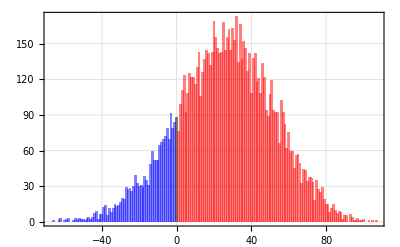

blue 15.69%    ev: 243.273

tie  0.88%

red 83.43%     ev: 294.727

```mathematica
(* module to simulate an election  *)
redTotal:=Module[{},
(* start from safe votes *)
red=192;
blue=155;
(*assign votes from swing states *)
OH;GA;WI;MI;PA;AZ;CO;NV;VA;AZ;CT;IL;ME;MN;NH;NM;NC;VI;
 (*If pull out a state---> give the votes to red or blue and assess the situation*)
Return[red]
]

(* run 10000 simulations and look at a histogram of the results *)
data=Table[redTotal-269,{10000}];
blueWinsData=TakeWhile[Sort[data],#<0&];
tieData=TakeWhile[Sort[Abs[data]],#==0&];
redWinsData=TakeWhile[Reverse[Sort[data]],#>0&];
Histogram[{blueWinsData,tieData,redWinsData},152,PlotRange->All,PlotTheme->"Detailed",ChartStyle->{Blue,Black,Red}]
Print[" blue ",100*Length[blueWinsData]/10000.,"%    ev: ",269.-Mean[data] ]
Print["  tie  ",100*Length[tieData]/10000.,"%"]
Print["  red ",100*Length[redWinsData]/10000.,"%     ev: ",269.+Mean[data]]
```

```mathematica
(*make different modules for different senario*)
(*due on 20th march*)
(*1 base senario + 3 senarios*)
(*group 8*)
```